```mathematica
{{M1,M2,M3,M4,M5,M6,M7,M8, N1, N2, N3, N4, N5, N6, N7, N8}}={m1, m2, m3, m4, m5, m6, m7, m8, n1, n2, n3, n4, n5, n6, n7, n8}/.FindInstance[(m1>n1>0&&(m6+m7)*(n7+n8)>(n6+n7)*(m7+m8))(*||
(n1>m1>0&&(m6+m7)*(n7+n8)<(n6+n7)*(m7+m8)))*)
&&(m2>n2>0&&(m5+m8)*(n7+n8)>(n5+n8)*(m7+m8))(*||
(n2>m2>0&&(m5+m8)*(n7+n8)<(n5+n8)*(m7+m8)))*)
&&(*(m3>n3>0&&(m5+m8)*(n5+n6)>(n5+n8)*(m5+m6))||*)
(n3>m3>0&&(m5+m8)*(n5+n6)<(n5+n8)*(m5+m6))
&&(m4>n4>0&&(m6+m7)*(n5+n6)>(n6+n7)*(m5+m6))(*||
(n4>m4>0&&(m6+m7)*(n5+n6)<(n6+n7)*(m5+m6))*)
&&(m5>n5>0&&(m2+m3)*(n3+n4)<(n2+n3)*(m3+m4))(*||
(n5>m5>0&&(m2+m3)*(n3+n4)>(n2+n3)*(m3+m4)))*)
&&(m6>n6>0&&(m1+m4)*(n3+n4)<(n1+n4)*(m3+m4))(*||
(n6>m6>0&&(m1+m4)*(n3+n4)>(n1+n4)*(m3+m4)))*)
&&(*(m7>n7>0&&(m1+m4)*(n1+n2)<(n1+n4)*(m1+m2))||*)
(n7>m7>0&&(m1+m4)*(n1+n2)>(n1+n4)*(m1+m2))
&&(m8>n8>0&&(m2+m3)*(n1+n2)<(n2+n3)*(m1+m2))(*||
(n8>m8>0&&(m2+m3)*(n1+n2)>(n2+n3)*(m1+m2))*)
(*&&Abs[m1-n1]<Min[{m5,n5}]*)
&&Abs[m2-n2]<Min[{m6,n6}]
(*&&Abs[m3-n3]<Min[{m7,n7}]*)
(*&&Abs[m4-n4]<Min[{m8,n8}]*)
(*&&Abs[m5-n5]<Min[{m1,n1}]*)
(*&&Abs[m6-n6]<Min[{m2,n2}]*)
&&Abs[m7-n7]<Min[{m3,n3}]
(*&&Abs[m8-n8]<Min[{m4,n4}]*)
,{m1,m2,m3,m4,m5,m6,m7,m8,n1,n2,n3,n4,n5,n6,n7,n8}]
{M1,M2,M3,M4,M5,M6,M7,M8}
{N1,N2,N3,N4,N5,N6,N7,N8}
```

{{4097/4096,5/4,3/128,353/512,17/16,1/2,1/64,1/64,1,1,17/128,1/2,1,7/16,1/32,1/256}}

{4097/4096,5/4,3/128,353/512,17/16,1/2,1/64,1/64}

{1,1,17/128,1/2,1,7/16,1/32,1/256}

```mathematica
kM1=(M6+M7)/(M7+M8)
kM5=(M2+M3)/(M3+M4)
kN1=(N6+N7)/(N7+N8)
kN5=(N2+N3)/(N3+N4)
```

33/2

652/365

40/3

145/81

```mathematica
kM2=-(M5+M8)/(M7+M8)
kM6=-(M1+M4)/(M3+M4)
kN2=-(N5+N8)/(N7+N8)
kN6=-(N1+N4)/(N3+N4)
```

-69/2

-6921/2920

-257/9

-64/27

```mathematica
kM3=(M5+M8)/(M5+M6)
kM7=(M1+M4)/(M1+M2)
kN3=(N5+N8)/(N5+N6)
kN7=(N1+N4)/(N1+N2)
```

69/100

6921/9217

257/368

3/4

```mathematica
kM4=-(M6+M7)/(M5+M6)
kM8=-(M2+M3)/(M1+M2)
kN4=-(N6+N7)/(N5+N6)
kN8=-(N2+N3)/(N1+N2)
```

-33/100

-5216/9217

-15/46

-145/256

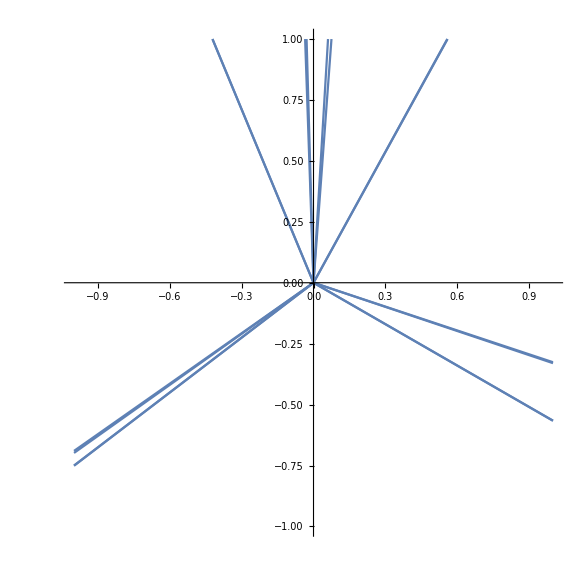

```mathematica
l1=ListPlot[{{0,0},{1/kM1,1}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l2=ListPlot[{{0,0},{1/kM5,1}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l3=ListPlot[{{0,0},{1/kN1,1}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l4=ListPlot[{{0,0},{1/kN5,1}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l5=ListPlot[{{0,0},{1/kM2,1}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l6=ListPlot[{{0,0},{1/kM6,1}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l7=ListPlot[{{0,0},{1/kN2,1}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l8=ListPlot[{{0,0},{1/kN6,1}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l9=ListPlot[{{0,0},{-1,-kM3}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l10=ListPlot[{{0,0},{-1,-kM7}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l11=ListPlot[{{0,0},{-1,-kN3}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l12=ListPlot[{{0,0},{-1,-kN7}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l13=ListPlot[{{0,0},{1,kM4}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l14=ListPlot[{{0,0},{1,kM8}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l15=ListPlot[{{0,0},{1,kN4}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
l16=ListPlot[{{0,0},{1,kN8}},Joined->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1];
Show[l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,l11,l12,l13,l14,l15,l16]
```